```mathematica
"パッケージmsh_tensorial.wlをダウンロードする。"
Names["mshtensorial`*"]
Remove["Global`*"]
packagefile="C:\\Users\\shina\\Desktop\\math_tensor\\msh_tensorial.wl";
"packagefile=wlファイルをおいているホルダーを記載\\msh_tensorial.wl" 
Needs["mshtensorial`",packagefile];
Names["Global`*"]
"パッケージ内いの関数と特殊文字を表記"
Names["mshtensorial`*"]
```

パッケージmsh_tensorial.wlをダウンロードする。

{}

Remove::rmnsm: "Global`*"に合致するシンボルはありません．

packagefile=wlファイルをおいているホルダーを記載\msh_tensorial.wl

{packagefile}

パッケージ内いの関数と特殊文字を表記

{AbsoluteDerivative,Christoffel1,Christoffel2,CovariantDerivative,DummyVariableSimplify,EinsteinTensor,EvaluateIndexDerivative,Expand2ndCODer,ExpandABSDer,ExpandChristoffel1,ExpandChristoffel2,ExpandCODer,ExpandDoubleIndex,ExpandIndex,ExpandMat,ExpandRCC,ExpandRiccFor,ExpandRicci,IndexDerivative,IndexDerivativeSimplify,IndexDerivativeUp,Kronecker,KroneckerSimplify,LeviCivitaRule,MatTen,MetricSimplify,NDim,OrderChristoffel2,OrderTensor,RCC,RiccFormula,RieChrisCur,SetSystem,SetTensorRule,Tensor,TensorSimplify,ToContravariantIndex,ToCovariantIndex,Void,x,Γ,δ,ϵ,ξ,ρ,σ}

## 第3 章 双対座標系

リーマン幾何学では、基底の長さが1 とは限らないため、計量テンソルが導入され、内積などの定義に、それが利用される。こうした計算を、さらに楽にするために導入された双対座標系という概念について説明する。

## 3.1 双対基底

### リーマン幾何学では、基底の長さが1 とは限らない。このため、ベクトルの内積や長さの計算に計量テンソルが必要であった。この面倒さを省くために導入されたのが双対基底という概念である。雰囲気を言えば、自然基底の逆数の長さを持つような基底である。双対基底（dual basis） ⟨e_(" ")^m⟩は厳密には次のように定義される．なお⟨e_n^(" ")⟩ は自然基底である。 (3.1)

```mathematica
Remove["Global`*"]
"(3.1)"
Tensor[e,{Void},{m}].Tensor[e,{n},{Void}]==Tensor[e,{n},{Void}].Tensor[e,{Void},{m}]==Kronecker[n,m]
Tensor[e,{m},{Void}].Tensor[e,{Void},{n}]==Tensor[e,{Void},{n}].Tensor[e,{m},{Void}]==Kronecker[n,m]
Tensor[e,{m},{Void}].Tensor[e,{n},{Void}]
```

(3-1)

e_^m.e_n^==e_n^.e_^m==δ_n^m

e_m^.e_^n==e_^n.e_m^==δ_n^m

e_m^.e_n^

### e_(" ")^mはすべての自然基底e_n^(" ") (n!= m) に直交した方向をとり、さらにe_m^(" ") の射影の逆数の長さを持つ。この結果、e_m^(" ").e_n^(" ")が必ずしもδ_n^m となることが保証されていなかった自然基底に対し、双対基底e_(" ")^m を利用することにより、通常のベクトル空間と同様な式を確立することができたのである。上式の最左辺と最右辺に、∂_(x_(" ")^m) (x̄)_(" ")^μ ∂_((x̄)_(" ")^ν) x_(" ")^mを掛ける。

```mathematica
ClearAttributes[Times,Orderless]
"("IndexDerivative[x̄[μ],x[m]]Tensor[e,{Void},{m}]")"."("IndexDerivative[x[n],x̄[ν]]Tensor[e,{n},{Void}]")"==IndexDerivative[x̄[μ],x[m]]IndexDerivative[x[n],x̄[ν]]Kronecker[n,m]==IndexDerivative[x̄[μ],x[m]]IndexDerivative[x[m],x̄[ν]]==Kronecker[ν,μ]
```

( ∂_(x_^m) (x̄)_^μ e_^m ).( ∂_((x̄)_^ν) x_^n e_n^ )==∂_(x_^m) (x̄)_^μ ∂_((x̄)_^ν) x_^n δ_n^m==∂_(x_^m) (x̄)_^μ ∂_((x̄)_^ν) x_^m==δ_ν^μ

### 自然基底の変換則はすでにわかっているので、左辺の∂_((x̄)_(" ")^ν) x_(" ")^n e_n^(" ") は (ē)_ν^(" ") にしてよい。

```mathematica
IndexDerivative[x̄[μ],x[m]]"("Tensor[e,{Void},{m}].Tensor[ē,{ν},{Void}]")"==Kronecker[ν,μ]
Tensor[ē,{Void},{μ}]Tensor[ē,{ν},{Void}]==Kronecker[ν,μ]
```

∂_(x_^m) (x̄)_^μ ( e_^m.(ē)_ν^ )==δ_ν^μ

(ē)_^μ (ē)_ν^==δ_ν^μ

### さて、変換先の座標系でも、(ē)_(" ")^μ (ē)_ν^(" ")==δ_ν^μが成立するはずであり、この式を満す (ē)_ν^(" ")は一意に決定されるはずである。 これと比較すると、

```mathematica
Tensor[ē,{Void},{ν}]==IndexDerivative[x̄[μ],x[m]]Tensor[e,{Void},{m}]
```

(ē)_^ν==∂_(x_^m) (x̄)_^μ e_^m

### なる双対基底の順方向の生成式が得られる。自然基底では反変逆変換係数（共変順変換係数）であったのに対し、反変順変換係数が生成係数となる。また、生成規則が反変的であるので、上付きのサフィックスを付ける。 この式から直ちに、双対基底の逆生成式も得られる。誘導は読者に一任する。

```mathematica
Tensor[e,{Void},{m}]==IndexDerivative[x[m],x̄[μ]]Tensor[ē,{Void},{μ}]
SetAttributes[Times,Orderless]
```

e_^m==∂_((x̄)_^μ) x_^m (ē)_^μ

### この変換は、反変逆変換係数による。

## 3.2 双対座標系の計量テンソル

### 双対基底em からも新たな計量テンソルg_(" "" ")^mn を定義することができる。

```mathematica
Tensor[g,{Void,Void},{m,n}]==Tensor[e,{Void},{m}].Tensor[e,{Void},{n}]
```

g_^mn==e_^m.e_^n

### このgmn の変換則は、双対基底の変換則を利用して求めることができる。

```mathematica
ClearAttributes[Times,Orderless]
Tensor[ḡ,{Void,Void},{μ,ν}]==Tensor[ē,{Void},{μ}].Tensor[ē,{Void},{ν}]=="("IndexDerivative[x̄[μ],x[m]] Tensor[e,{Void},{m}]")"."("IndexDerivative[x̄[ν],x[n]] Tensor[e,{Void},{n}]")"==IndexDerivative[x̄[μ],x[m]]IndexDerivative[x̄[ν],x[n]]"("Tensor[e,{Void},{m}].Tensor[e,{Void},{n}]")"==IndexDerivative[x[m],x̄[μ]]IndexDerivative[x̄[ν],x[n]]Tensor[g,{Void,Void},{m,n}]
```

(ḡ)_^μν==(ē)_^μ.(ē)_^ν==( ∂_(x_^m) (x̄)_^μ e_^m ).( ∂_(x_^n) (x̄)_^ν e_^n )==∂_(x_^m) (x̄)_^μ ∂_(x_^n) (x̄)_^ν ( e_^m.e_^n )==∂_((x̄)_^μ) x_^m ∂_(x_^n) (x̄)_^ν g_^mn

### この変換則からわかるように、 g_(" "" ")^mnはテンソルの反変成分である。 計量テンソルg_(m" ")^(" "n)も定義できる。

```mathematica
Tensor[g,{m,Void},{Void,n}]==Tensor[e,{m},{Void}].Tensor[e,{Void},{n}]==Tensor[e,{Void},{n}].Tensor[e,{m},{Void}]==Kronecker[m,n]
```

g_m^n==e_m^.e_^n==e_^n.e_m^==δ_m^n

### g_(m" ")^(" "n)の変換則も基底の変換則から求めることができる。

```mathematica
ClearAttributes[Times,Orderless]
Tensor[ḡ,{μ,Void},{Void,ν}]==Tensor[ē,{μ},{Void}].Tensor[ē,{Void},{ν}]=="("IndexDerivative[x[m],x̄[μ]] Tensor[e,{m},{Void}]")"."("IndexDerivative[x̄[ν],x[n]] Tensor[e,{Void},{n}]")"==IndexDerivative[x[m],x̄[μ]]IndexDerivative[x̄[ν],x[n]]"("Tensor[e,{m},{Void}].Tensor[e,{Void},{n}]")"==IndexDerivative[x[m],x̄[μ]]IndexDerivative[x̄[ν],x[n]]Tensor[g,{m,Void},{Void,n}]==Kronecker[μ,ν]
"単位行列"
Tensor[g,{m,n},{Void,Void}]
SetAttributes[Times,Orderless]
```

(ḡ)_μ^ν==(ē)_μ^.(ē)_^ν==( ∂_((x̄)_^μ) x_^m e_m^ ).( ∂_(x_^n) (x̄)_^ν e_^n )==∂_((x̄)_^μ) x_^m ∂_(x_^n) (x̄)_^ν ( e_m^.e_^n )==∂_((x̄)_^μ) x_^m ∂_(x_^n) (x̄)_^ν g_m^n==δ_μ^ν

単位行列

g_mn^

### ここには、反変逆変換係数と反変順変換係数が混ざって入っているため、g_(m" ")^(" "n)はテンソルの混合成分である。 これで、計量テンソルg の共変成分g_mn^(" "" ")、混合成分g_(m" ")^(" "n)、反変成分g_(" "" ")^mn が揃ったことになる。

## 3.3 共変ベクトル

### この双対基底を使って、任意のベクトルA を展開してみよう。

```mathematica
Style[A,FontSize->16]==Tensor[A,{m},{Void}]Tensor[e,{Void},{m}]
```

A==A_m^ e_^m

### 前節と同様な手順で、次の変換則が得られる。(3.2)

```mathematica
ClearAttributes[Times,Orderless]
"(3.2)"
Tensor[A,{μ},{Void}]==Tensor[A,{m},{Void}]IndexDerivative[x[m],x̄[μ]]
```

A_μ^==A_m^ ∂_((x̄)_^μ) x_^m

### ベクトルA の e_(" ")^m の成分A_m^(" ")は、自然基底e_(" ")^m と同じ変換を受けるため、ベクトルの共変成分（covariant component）と呼ばれ、下付きのサフィックスを付ける。なお、ベクトルの共変成分は、他書では共変ベクトル（covariant vector）と記載されているが、本書ではその意味を考え、あえて共変成分と表現した。 式(3.2) の∂_((x̄)_(" ")^μ) x_(" ")^mをm 行μ 列の行列に対応させるとすると、(Ā)_μ^(" ")などは横ベクトルに対応させるべきである。

```mathematica
NDim=5;
⟨Tensor[Ā,{μ},{Void}]⟩==⟨Tensor[A,{m},{Void}]⟩.⟨IndexDerivative[x[m],x̄[μ]]⟩
MatrixForm[{ExpandIndex[%[[1,1]],{μ}]}]==MatrixForm[{ExpandIndex[%[[2,1,1]],{m}]}].MatrixForm[ExpandIndex[%[[2,2,1]],{m,μ}]]
```

⟨(Ā)_μ^⟩==⟨A_m^⟩.⟨∂_((x̄)_^μ) x_^m⟩

((Ā)_1^ | (Ā)_2^ | (Ā)_3^ | (Ā)_4^ | (Ā)_5^)==(A_1^ | A_2^ | A_3^ | A_4^ | A_5^).(∂_((x̄)_^1) x_^1 | ∂_((x̄)_^2) x_^1 | ∂_((x̄)_^3) x_^1 | ∂_((x̄)_^4) x_^1 | ∂_((x̄)_^5) x_^1
∂_((x̄)_^1) x_^2 | ∂_((x̄)_^2) x_^2 | ∂_((x̄)_^3) x_^2 | ∂_((x̄)_^4) x_^2 | ∂_((x̄)_^5) x_^2
∂_((x̄)_^1) x_^3 | ∂_((x̄)_^2) x_^3 | ∂_((x̄)_^3) x_^3 | ∂_((x̄)_^4) x_^3 | ∂_((x̄)_^5) x_^3
∂_((x̄)_^1) x_^4 | ∂_((x̄)_^2) x_^4 | ∂_((x̄)_^3) x_^4 | ∂_((x̄)_^4) x_^4 | ∂_((x̄)_^5) x_^4
∂_((x̄)_^1) x_^5 | ∂_((x̄)_^2) x_^5 | ∂_((x̄)_^3) x_^5 | ∂_((x̄)_^4) x_^5 | ∂_((x̄)_^5) x_^5)

### どんなベクトルからも、反変成分も共変成分も求めることができる。例えば、微小ベクトル dx_^ も自然基底em で展開せずに、双対基底 e_(" ")^m で展開すれば、共変成分dx_m^(" ")が得られる。

```mathematica
Tensor[dx,{},{}]==Tensor[dx,{m},{Void}]Tensor[e,{Void},{m}]
```

dx_^==dx_m^ e_^m

### 元々、共変成分を使ってベクトルを定義した方がよいものとして、任意のスカラー関数f の空間微分商がある*1。これは、自然基底が分母に入るからである。∂_(x_(" ")^m) fを変換してみよう。

```mathematica
ClearAttributes[Times,Orderless]
IndexDerivative[f,x̄[μ]]=="("IndexDerivative[f,x[m]]")"IndexDerivative[x[m],x̄[μ]]
```

∂_((x̄)_^μ) f==( ∂_(x_^m) f ) ∂_((x̄)_^μ) x_^m

### *1 単に微分と呼ぶと、df も∂_x f のいずれを指すかがわからないので、df のような微小量を微分、∂_x f のような微分演算の結果を微分商と呼ぶこととする。

```mathematica
IndexDerivative[f,x]
```

∂_x f

### これが、∂_(x_(" ")^m) fの順変換である。この式を式(3.2) と比較してみると、同じ形をしており、変換 係数が、反変逆変換係数になっていることに着目してほしい。このため、∂_(x_(" ")^m) fは共変成分とし ての変換を受ける。逆変換は次のようになる。

```mathematica
IndexDerivative[f,x[m]]=="("IndexDerivative[f,x̄[μ]]")"IndexDerivative[x̄[μ],x[m]]
```

∂_(x_^m) f==( ∂_((x̄)_^μ) f ) ∂_(x_^m) (x̄)_^μ

### 詳細は次節で説明するが、∂_(x_(" ")^m) fから反変成分を求めることも可能である。その場合には ("∂")_f^(x_(" ")^m) と書き、反変成分となる。

```mathematica
IndexDerivativeUp[f,x[m]]
```

∂_f^(x_^m)

### [例3.1] [デカルト座標系の双対基底] デカルト座標系では次式が成立する。

```mathematica
Tensor[e,{m},{Void}].Tensor[e,{n},{Void}]==Tensor[δ,{m,n},{Void,Void}]==Kronecker[n,m]
```

e_m^.e_n^==δ_mn^==δ_n^m

#### これと式(3.1) を比較すると、δ_mn^(" "" ") とδ_n^m は同じ内容であるので、

```mathematica
Tensor[e,{Void},{m}]==Tensor[e,{m},{Void}]
```

e_^m==e_m^

#### であることがわかる。つまり、デカルト座標系では双対基底は自然基底と同じである。その結果dx_(" ")^m==dx_m^(" ")も成立する。これはデカルト座標系でのみ成立する。さらに計量テンソルは次のようになる。

```mathematica
Tensor[dx,{Void},{m}]==Tensor[dx,{m},{Void}]
⟨Tensor[g,{m,n},{Void,Void}]⟩==⟨Tensor[g,{m,Void},{Void,n}]⟩==⟨Tensor[g,{Void,Void},{m,n}]⟩==DiagonalMatrix[{1,1,1}]
```

dx_^m==dx_m^

⟨g_mn^⟩==⟨g_m^n⟩==⟨g_^mn⟩=={{1,0,0},{0,1,0},{0,0,1}}

### [例3.2] [斜交座標系の双対基底] 例2.6 に示した斜交座標系の双対基底を考えてみよう。双対基底は式(3.1) に示した自然基底との正規直交関係から誘導するのが筋であろうが、デカルト座標系との変換がわかっている場合には、デカルト座標系の双対基底から誘導する方法がある。幸いにして、デカルト座標系における双対基底は自然基底と一致しているので、これは楽な方法である。 この関係式は、式(2.8) に誘導した反変順変換係数が使われ、次のようになる。

```mathematica
Tensor[ē,{x},{Void}]==Tensor[ē,{1},{Void}]==IndexDerivative[x̄[1],x[1]]Tensor[e,{Void},{1}]+IndexDerivative[x̄[1],x[2]]Tensor[e,{Void},{2}]==0.8 Tensor[e,{Void},{1}]-0.4Tensor[e,{Void},{2}]
Tensor[ē,{y},{Void}]==Tensor[ē,{2},{Void}]==IndexDerivative[x̄[2],x[1]]Tensor[e,{Void},{1}]+IndexDerivative[x̄[2],x[2]]Tensor[e,{Void},{2}]==-0.4 Tensor[e,{Void},{1}]+1.2Tensor[e,{Void},{2}]
```

(ē)_x^==(ē)_1^==∂_(x_^1) (x̄)_^1 e_^1+∂_(x_^2) (x̄)_^1 e_^2==0.8 e_^1-0.4 e_^2

(ē)_y^==(ē)_2^==∂_(x_^1) (x̄)_^2 e_^1+∂_(x_^2) (x̄)_^2 e_^2==-0.4 e_^1+1.2 e_^2

#### -Graphics-

#### これら双対基底を図3.1 に示すが、⟨(ē)_(" ")^μ⟩ と ⟨(ē)_μ^(" ")⟩の内積が正規直交していることが読み取れよう。 また、基準としているデカルト座標系で(2, 1) の値を持つA なるベクトルが（デカルト座標系では共変成分は反変成分と等しい）、双対座標系で次のような大きな成分を持つことも読み取れよう。

```mathematica
⟨Tensor[ē,{Void},{μ}]⟩.⟨Tensor[ē,{μ},{Void}]⟩==Kronecker[μ,μ]

⟨Tensor[Ā,{μ},{Void}]⟩==⟨IndexDerivative[x[m],x̄[μ]]Tensor[A,{m},{Void}]⟩==⟨Tensor[A,{m},{Void}]⟩.⟨IndexDerivative[x[m],x̄[μ]]⟩==MatrixForm[{{2,1}}].MatrixForm[{{1.5,0.5},{0.5,1}}]=={2,1}.{{1.5,0.5},{0.5,1}}
⟨Tensor[Ā,{Void},{μ}]⟩==⟨IndexDerivative[x̄[μ],x[m]]Tensor[A,{Void},{m}]⟩==⟨Tensor[A,{Void},{m}]⟩.⟨IndexDerivative[x̄[μ],x[m]]⟩=={2,1}.Inverse[{{1.5,0.5},{0.5,1}}]
```

⟨(ē)_^μ⟩.⟨(ē)_μ^⟩==δ_μ^μ

⟨(Ā)_μ^⟩==⟨∂_((x̄)_^μ) x_^m A_m^⟩==⟨A_m^⟩.⟨∂_((x̄)_^μ) x_^m⟩==(2 | 1).(1.5 | 0.5
0.5 | 1)=={3.5,2.}

⟨(Ā)_^μ⟩==⟨∂_(x_^m) (x̄)_^μ A_^m⟩==⟨A_^m⟩.⟨∂_(x_^m) (x̄)_^μ⟩=={1.2,0.4}

#### これからA の二乗長を計算することができる。

```mathematica
Tensor[Ā,{μ},{Void}]Tensor[Ā,{Void},{μ}]=={1.2,0.4}.{3.5,2}
```

(Ā)_^μ (Ā)_μ^==5.

#### g_(" "" ")^μνは次のようになる。

```mathematica
NDim=2;
ClearAttributes[Times,Orderless]
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==⟨IndexDerivative[x̄[μ],x[m]]Tensor[g,{Void,Void},{m,n}]IndexDerivative[x̄[ν],x[n]]⟩
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==⟨IndexDerivative[x̄[μ],x[m]]Kronecker[m,n]IndexDerivative[x̄[ν],x[n]]⟩
%[[1]]==MatrixForm[ExpandIndex[%[[2,1,1]],{μ,m}]].MatrixForm[ExpandIndex[%[[2,1,2]],{n,m}]]. MatrixForm[ExpandIndex[%[[2,1,3]],{ν,n}]]^T
%[[1]]==MatrixForm[{{0.8,-0.4},{-0.4,1.2}}].MatrixForm[{{0.8,-0.4},{-0.4,1.2}}]^T
%[[1]]==MatrixForm[%[[2,1,1]].%[[2,2,1,1]]ᵀ]
```

⟨(ḡ)_^μν⟩==⟨∂_(x_^m) (x̄)_^μ g_^mn ∂_(x_^n) (x̄)_^ν⟩

⟨(ḡ)_^μν⟩==⟨∂_(x_^m) (x̄)_^μ δ_m^n ∂_(x_^n) (x̄)_^ν⟩

⟨(ḡ)_^μν⟩==(∂_(x_^1) (x̄)_^1 | ∂_(x_^2) (x̄)_^1
∂_(x_^1) (x̄)_^2 | ∂_(x_^2) (x̄)_^2).(1 | 0
0 | 1).((∂_(x_^1) (x̄)_^1 | ∂_(x_^2) (x̄)_^1
∂_(x_^1) (x̄)_^2 | ∂_(x_^2) (x̄)_^2))^T

⟨(ḡ)_^μν⟩==(0.8 | -0.4
-0.4 | 1.2).((0.8 | -0.4
-0.4 | 1.2))^T

⟨(ḡ)_^μν⟩==(0.8 | -0.8
-0.8 | 1.6)

#### さらに、(ḡ)_μν^(" "" ")の昇階と言ってもよいし、(ḡ)_(" "" ")^μν の降階と言ってもよいが、(ḡ)_μκ^(" "" ") (ḡ)_(" "" ")^κν′を計算すると、期待通りδ_μ^ν が得られる。

```mathematica
Tensor[ḡ,{μ,ν},{Void,Void}]
Tensor[ḡ,{μ,κ},{Void,Void}]Tensor[ḡ,{Void,Void},{κ,ν}]==MatrixForm[{{2.5,1.25},{1.25,1.25}}].MatrixForm[{{0.8,-0.8},{-0.8,1.6}}]
%[[1]]==MatrixForm[%[[2,1,1]].%[[2,2,1]]]==Kronecker[μ,ν]
```

(ḡ)_μν^

(ḡ)_^κν (ḡ)_μκ^==(2.5 | 1.25
1.25 | 1.25).(0.8 | -0.8
-0.8 | 1.6)

(ḡ)_^κν (ḡ)_μκ^==(1. | 0.
0. | 1.)==δ_μ^ν

### [例3.3] [勾配ベクトル] 空間微分商の直感的理解を得るために、図3.2 を見てほしい。先と同じ直線座標系で、今度はf の等高線が記載してある。まず、基準となるデカルト座標系ではe_x^(" ")==e_1^(" ") 方向に1 動くとf は2 増えるから、∂_(x_(" ")^1) f = 2、また e_y^(" ")==e_2^(" ")方向に1 動くとf は1 増えるから、∂_(x_(" ")^2) f は1 である。このためデカルト座標系におけるベクトルは図にA として示した{A_x^(" "),A_y^(" ")}=={A_1^(" "),A_2^(" ")}== (2, 1) である。 変換後の直線座標系では、自然基底の(ē)_x^(" ")==(ē)_1^(" ")方向へ1 移動するとf は3.5 増え、(ē)_y^(" ")==(ē)_2^(" ") 方向へ1移動するとf は2 増えるので、 ∂_((x̄)_(" ")^1) fは3.5、∂_((x̄)_(" ")^2) f は2 である。しかし自然基底で見ると(3.5, 2) なるベクトルは元のベクトルとは一致しない。これを双対基底系の(3.5, 2) ベクトルだと思うと一致するのである（実は、このA や基底は、前の例の値に合せてあるので、簡単に比較可能である）。 反変の微分商("∂")_f^(x_(" ")^m)==g_(" "" ")^mn ∂_(x_(" ")^n) fは双対基底の方へ移動することで、その成分を計算することができ、上記と同様の考察が可能である。作業は読者に任せる。

```mathematica
Tensor[e,{x},{Void}]==Tensor[e,{1},{Void}];
Tensor[e,{y},{Void}]==Tensor[e,{2},{Void}];
Tensor[ē,{x},{Void}]==Tensor[ē,{1},{Void}];
Tensor[ē,{y},{Void}]==Tensor[ē,{2},{Void}];
r1={f->2 x[1]+x[2]}
{Tensor[A,{x},{Void}],Tensor[A,{y},{Void}]}=={Tensor[A,{1},{Void}],Tensor[A,{2},{Void}]}=={IndexDerivative[f,x[1]],
IndexDerivative[f,x[2]]}
{Tensor[A,{1},{Void}],Tensor[A,{2},{Void}]}=={IndexDerivative[f,x[1]],
IndexDerivative[f,x[2]]}/.r1
%[[1]]==EvaluateIndexDerivative[%[[2]]]

r2={f->3.5 x̄[1]+2 x̄[2]}
{Tensor[Ā,{x},{Void}],Tensor[Ā,{y},{Void}]}=={Tensor[Ā,{1},{Void}],Tensor[Ā,{2},{Void}]}=={IndexDerivative[f,x̄[1]],
IndexDerivative[f,x̄[2]]}
{Tensor[Ā,{1},{Void}],Tensor[Ā,{2},{Void}]}=={IndexDerivative[f,x̄[1]],
IndexDerivative[f,x̄[2]]}/.r2
%[[1]]==EvaluateIndexDerivative[%[[2]]]

IndexDerivativeUp[f,x[μ]]==Tensor[g,{Void,Void},{μ,ν}]IndexDerivative[f,x[ν]]
⟨IndexDerivativeUp[f,x[μ]]⟩==⟨Tensor[g,{Void,Void},{μ,ν}]⟩.⟨IndexDerivative[f,x̄[ν]]⟩
⟨IndexDerivativeUp[f,x[μ]]⟩==MatrixForm[{{0.8,-0.8},{-0.8,1.6}}].MatrixForm[{3.5,2}]
{Tensor[Ā,{Void},{1}],Tensor[Ā,{Void},{2}]}==%[[2,1,1]].%[[2,2,1]]
SetAttributes[Times,Orderless]
```

{f→2 x_^1+x_^2}

{A_x^,A_y^}=={A_1^,A_2^}=={∂_(x_^1) f,∂_(x_^2) f}

{A_1^,A_2^}=={2 ∂_(x_^1) x_^1+∂_(x_^1) x_^2,2 ∂_(x_^2) x_^1+∂_(x_^2) x_^2}

{A_1^,A_2^}=={2,1}

{f→3.5 (x̄)_^1+2 (x̄)_^2}

{(Ā)_x^,(Ā)_y^}=={(Ā)_1^,(Ā)_2^}=={∂_((x̄)_^1) f,∂_((x̄)_^2) f}

{(Ā)_1^,(Ā)_2^}=={3.5 ∂_((x̄)_^1) (x̄)_^1+2 ∂_((x̄)_^1) (x̄)_^2,3.5 ∂_((x̄)_^2) (x̄)_^1+2 ∂_((x̄)_^2) (x̄)_^2}

{(Ā)_1^,(Ā)_2^}=={3.5,2.}

∂_f^(x_^μ) ==∂_(x_^ν) f g_^μν

⟨∂_f^(x_^μ) ⟩==⟨g_^μν⟩.⟨∂_((x̄)_^ν) f⟩

⟨∂_f^(x_^μ) ⟩==(0.8 | -0.8
-0.8 | 1.6).(3.5
2)

{(Ā)_^1,(Ā)_^2}=={1.2,0.4}

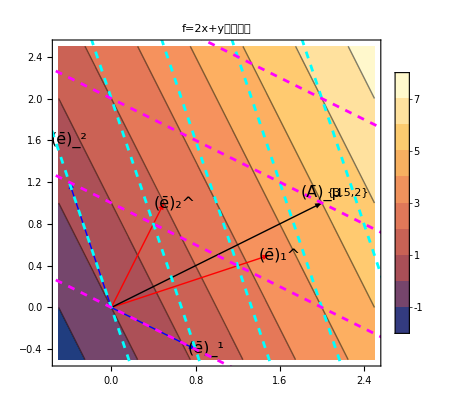

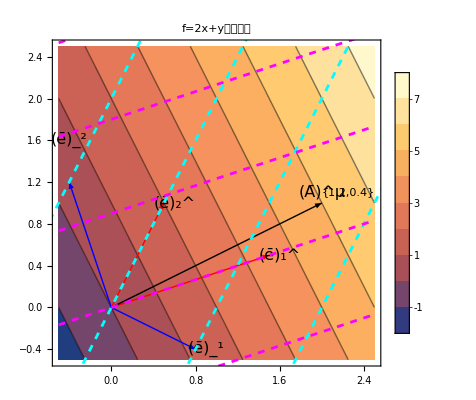

```mathematica
g1=ContourPlot[2x +y,{x,-0.5,2.5},{y,-0.5,2.5},PlotLegends->Automatic,Axes->True,AxesStyle->Directive[Black,Thick],PlotLabel->"f=2x+yの等高線"];
g2=Graphics[{Red,Arrow[{{0,0},{1.5,0.5}}],Arrow[{{0,0},{0.5,1}}],Black,Arrow[{{0,0},{2,1}}]}];
g3=Graphics[{Text[Tensor[ē,{1},{Void}],{1.6,0.5}],Text[Tensor[ē,{2},{Void}],{0.6,1}]}];
g31=Graphics[{Text[Tensor[Ā,{μ},{}] ,{2,1.1}],Text[{3.5,2} ,{2.25,1.1}]}];
g32=Graphics[{Text[Tensor[Ā,{},{μ}],{2,1.1}],Text[{1.2,0.4} ,{2.25,1.1}]}];
g4=Graphics[{Blue,Arrow[{{0,0},{0.8,-0.4}}],Arrow[{{0,0},{-0.4,1.2}}]}];
g5=Graphics[{Text[Tensor[ē,{Void},{1}],{0.9,-0.4}],Text[Tensor[ē,{Void},{2}],{-0.4,1.6}]}];
g6=Plot[Table[-3x+2a,{a,0,4}],{x,-1,4},PlotStyle->{Cyan,Dashed}];
g7=Plot[Table[-.5x+a,{a,0,4}],{x,-1,4},PlotStyle->{Magenta,Dashed}];
g8=Plot[Table[2x+2a,{a,-4,2}],{x,-1,4},PlotStyle->{Cyan,Dashed}];
g9=Plot[Table[1/3x+0.9a,{a,-1,4}],{x,-0.5,2.5},PlotStyle->{Magenta,Dashed}];
Show[g1,g2,g3,g4,g5,g6,g7,g31]
Show[g1,g2,g3,g4,g5,g8,g9,g32]
```

#### -Graphics-

### [例3.4] [二次元極座標系] 自然基底については、例2.7 に示した変換式(2.10) が成立する。

```mathematica
Remove["Global`*"]
NDim=2;
SetAttributes[Times,Orderless]
Tensor[ē,{r},{Void}]==Cos[ϕ]Tensor[e,{x},{Void}]+Sin[ϕ]Tensor[e,{y},{Void}]
Tensor[ē,{ϕ},{Void}]==-r Sin[ϕ]Tensor[e,{x},{Void}]+r Cos[ϕ]Tensor[e,{y},{Void}]
r1={x[1]->x̄[1]Cos[x̄[2]],x[2]->x̄[1]Sin[x̄[2]]}
Tensor[ē,{μ},{Void}]==IndexDerivative[x[m],x̄[μ]]Tensor[e,{m},{Void}]
MatrixForm[ExpandIndex[%[[1]],{μ}]]==MatrixForm[{ExpandIndex[%[[2,2]],{m}]}].MatrixForm[ExpandIndex[%[[2,1]],{m,μ}]]
s1=%[[1]]==%[[2,1]].MatrixForm[EvaluateIndexDerivative[%[[2,2,1]]/.r1]]
%[[1]]==MatrixForm[%[[2,1,1,1]].%[[2,2,1]]]
```

(ē)_r^==Cos[ϕ] e_x^+Sin[ϕ] e_y^

(ē)_ϕ^==-r Sin[ϕ] e_x^+r Cos[ϕ] e_y^

{x_^1→Cos[(x̄)_^2] (x̄)_^1,x_^2→Sin[(x̄)_^2] (x̄)_^1}

(ē)_μ^==∂_((x̄)_^μ) x_^m e_m^

((ē)_1^
(ē)_2^)==(e_1^ | e_2^).(∂_((x̄)_^1) x_^1 | ∂_((x̄)_^2) x_^1
∂_((x̄)_^1) x_^2 | ∂_((x̄)_^2) x_^2)

((ē)_1^
(ē)_2^)==(e_1^ | e_2^).(Cos[(x̄)_^2] | -Sin[(x̄)_^2] (x̄)_^1
Sin[(x̄)_^2] | Cos[(x̄)_^2] (x̄)_^1)

((ē)_1^
(ē)_2^)==(Cos[(x̄)_^2] e_1^+Sin[(x̄)_^2] e_2^
-Sin[(x̄)_^2] e_1^ (x̄)_^1+Cos[(x̄)_^2] e_2^ (x̄)_^1)

#### 双対基底はこれらと正規直交性が成立しないといけない。簡単に言えば、同じ方向を向き、長 さが逆数のベクトルを定義すればよい。

```mathematica
Tensor[ē,{Void},{μ}]==IndexDerivative[x̄[μ],x[m]]Tensor[e,{Void},{m}]
⟨Tensor[ē,{Void},{μ}]⟩==⟨IndexDerivative[x[m],x̄[μ]]⟩^(-1).⟨Tensor[e,{Void},{m}]
⟩

MatrixForm[ExpandIndex[%[[1,1]],{μ}]]==MatrixForm[ExpandIndex[%[[2,1,1,1]],{m,μ}]]^(-1).MatrixForm[ExpandIndex[%[[2,2,1]],{m}]]
s2=%[[1]]==MatrixForm[Inverse[EvaluateIndexDerivative[%[[2,1,1,1]]/.r1]]//Simplify].%[[2,2]]
%[[1]]==MatrixForm[%[[2,1,1]].%[[2,2,1]]]
```

(ē)_^μ==∂_(x_^m) (x̄)_^μ e_^m

⟨(ē)_^μ⟩==(⟨∂_((x̄)_^μ) x_^m⟩)^-1.⟨e_^m⟩

((ē)_^1
(ē)_^2)==((∂_((x̄)_^1) x_^1 | ∂_((x̄)_^2) x_^1
∂_((x̄)_^1) x_^2 | ∂_((x̄)_^2) x_^2))^-1.(e_^1
e_^2)

((ē)_^1
(ē)_^2)==(Cos[(x̄)_^2] | Sin[(x̄)_^2]
-Sin[(x̄)_^2]/((x̄)_^1) | Cos[(x̄)_^2]/((x̄)_^1)).(e_^1
e_^2)

((ē)_^1
(ē)_^2)==(Cos[(x̄)_^2] e_^1+Sin[(x̄)_^2] e_^2
-(Sin[(x̄)_^2] e_^1)/((x̄)_^1)+(Cos[(x̄)_^2] e_^2)/((x̄)_^1))

#### またベクトルの共変成分の変換式は自然基底の変換式と同じになる。

```mathematica
⟨Tensor[Ā,{μ},{Void}]⟩==⟨Tensor[A,{m},{Void}]⟩.s1[[2,2]]
MatrixForm[ExpandIndex[%[[1,1]],{μ}]]==MatrixForm[{ExpandIndex[%[[2,1,1]],{m}]}].s1[[2,2]]
```

⟨(Ā)_μ^⟩==⟨A_m^⟩.(Cos[(x̄)_^2] | -Sin[(x̄)_^2] (x̄)_^1
Sin[(x̄)_^2] | Cos[(x̄)_^2] (x̄)_^1)

((Ā)_1^
(Ā)_2^)==(A_1^ | A_2^).(Cos[(x̄)_^2] | -Sin[(x̄)_^2] (x̄)_^1
Sin[(x̄)_^2] | Cos[(x̄)_^2] (x̄)_^1)

#### (ḡ)_(" "" ")^μν を求めてみよう(μ, ν は極座標系側)。

```mathematica
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==⟨IndexDerivative[x[μ],x[m]]⟩.⟨Tensor[g,{Void,Void},{m,n}]⟩.⟨IndexDerivative[x[ν],x[n]]⟩
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==s2[[2,1]].s2[[2,1]]^T
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==%[[2,1,1]].%[[2,2,1,1]]ᵀ//Simplify
```

⟨(ḡ)_^μν⟩==⟨∂_(x_^m) x_^μ⟩.⟨g_^mn⟩.⟨∂_(x_^n) x_^ν⟩

⟨(ḡ)_^μν⟩==(Cos[(x̄)_^2] | Sin[(x̄)_^2]
-Sin[(x̄)_^2]/((x̄)_^1) | Cos[(x̄)_^2]/((x̄)_^1)).((Cos[(x̄)_^2] | Sin[(x̄)_^2]
-Sin[(x̄)_^2]/((x̄)_^1) | Cos[(x̄)_^2]/((x̄)_^1)))^T

⟨(ḡ)_^μν⟩=={{1,0},{0,((x̄)_^1)^-2}}

#### これは、(ē)_(" ")^r==(ē)_(" ")^1 の長さが1 なのに対し、(ē)_(" ")^ϕ==(ē)_(" ")^2の長さは1/r であること、それ故、ベクトルの長さに対し、(Ā)_ϕ^(" ")は1/r 倍の寄与があることを示している。前節の例とこの例に対し、r が極めて大きい場合の略図を描くことにより、自然基底と双対基底の直交関係や任意ベクトルの成分の概要を理解することができるので、ぜひトライしてほしい。

```mathematica
Tensor[ē,{Void},{r}]==Tensor[ē,{Void},{1}]==Tensor[ē,{1},{Void}]
Tensor[ē,{Void},{ϕ}]==Tensor[ē,{Void},{2}]==1/r^2 Tensor[ē,{2},{Void}]
Tensor[Ā,{ϕ},{Void}]
Tensor[ē,{Void},{1}].Tensor[ē,{1},{Void}]==1
Tensor[ē,{Void},{2}].Tensor[ē,{2},{Void}]==1/r^2|Tensor[ē,{2},{Void}]|^2==1
```

(ē)_^r==(ē)_^1==(ē)_1^

(ē)_^ϕ==(ē)_^2==((ē)_2^)/(r)^2

(Ā)_ϕ^

(ē)_^1.(ē)_1^==1

(ē)_^2.(ē)_2^==((|(ē)_2^|)^2)/(r)^2==1

### [例3.5] [球面幾何学] 自然基底については、例2.9 に示した変換式(2.12) が成立する。

```mathematica
Remove["Global`*"]
NDim=2;
SetAttributes[Times,Orderless]
r1={x[1]->a Sin[x̄[1]] Cos[x̄[2]],x[2]->a Sin[x̄[1]] Sin[x̄[2]],x[3]->a Cos[x̄[1]]}
⟨IndexDerivative[x[M],x̄[μ]]⟩==Table[IndexDerivative[x[M],x̄[μ]],{M,1,3},{μ,1,2}]/.r1
s1=⟨IndexDerivative[x[M],x̄[μ]]⟩==MatrixForm[EvaluateIndexDerivative[%[[2]]]]
MatrixForm[ExpandIndex[Tensor[ē,{μ},{Void}],{μ}]]==MatrixForm[Table[Tensor[e,{M},{Void}],{M,1,3}].s1[[2,1]]]
```

{x_^1→a Cos[(x̄)_^2] Sin[(x̄)_^1],x_^2→a Sin[(x̄)_^1] Sin[(x̄)_^2],x_^3→a Cos[(x̄)_^1]}

⟨∂_((x̄)_^μ) x_^M⟩=={{Cos[(x̄)_^2] ∂_((x̄)_^1) a Sin[(x̄)_^1]+a (Cos[(x̄)_^2] ∂_((x̄)_^1) Sin[(x̄)_^1]-∂_((x̄)_^1) (x̄)_^2 Sin[(x̄)_^1] Sin[(x̄)_^2]),Cos[(x̄)_^2] ∂_((x̄)_^2) a Sin[(x̄)_^1]+a (Cos[(x̄)_^1] Cos[(x̄)_^2] ∂_((x̄)_^2) (x̄)_^1+∂_((x̄)_^2) Cos[(x̄)_^2] Sin[(x̄)_^1])},{∂_((x̄)_^1) a Sin[(x̄)_^1] Sin[(x̄)_^2]+a (Cos[(x̄)_^2] ∂_((x̄)_^1) (x̄)_^2 Sin[(x̄)_^1]+∂_((x̄)_^1) Sin[(x̄)_^1] Sin[(x̄)_^2]),∂_((x̄)_^2) a Sin[(x̄)_^1] Sin[(x̄)_^2]+a (∂_((x̄)_^2) Sin[(x̄)_^2] Sin[(x̄)_^1]+Cos[(x̄)_^1] ∂_((x̄)_^2) (x̄)_^1 Sin[(x̄)_^2])},{Cos[(x̄)_^1] ∂_((x̄)_^1) a+a ∂_((x̄)_^1) Cos[(x̄)_^1],Cos[(x̄)_^1] ∂_((x̄)_^2) a-a ∂_((x̄)_^2) (x̄)_^1 Sin[(x̄)_^1]}}

⟨∂_((x̄)_^μ) x_^M⟩==(a Cos[(x̄)_^1] Cos[(x̄)_^2] | -a Sin[(x̄)_^1] Sin[(x̄)_^2]
a Cos[(x̄)_^1] Sin[(x̄)_^2] | a Cos[(x̄)_^2] Sin[(x̄)_^1]
-a Sin[(x̄)_^1] | 0)

((ē)_1^
(ē)_2^)==(a Cos[(x̄)_^1] Cos[(x̄)_^2] e_1^+a Cos[(x̄)_^1] Sin[(x̄)_^2] e_2^-a Sin[(x̄)_^1] e_3^
-a Sin[(x̄)_^1] Sin[(x̄)_^2] e_1^+a Cos[(x̄)_^2] Sin[(x̄)_^1] e_2^)

#### これらの逆変換は存在しない。したがって双対基底については、順変換はなく、これらの係数で逆変換を受けることとなる。

```mathematica
MatrixForm[Table[Tensor[e,{Void},{M}],{M,1,3}]]==MatrixForm[s1[[2,1]]].MatrixForm[ExpandIndex[Tensor[e,{μ},{Void}],{μ}]]
MatrixForm[Table[Tensor[e,{Void},{M}],{M,1,3}]]==MatrixForm[s1[[2,1]].ExpandIndex[Tensor[e,{μ},{Void}],{μ}]]
```

(e_^1
e_^2
e_^3)==(a Cos[(x̄)_^1] Cos[(x̄)_^2] | -a Sin[(x̄)_^1] Sin[(x̄)_^2]
a Cos[(x̄)_^1] Sin[(x̄)_^2] | a Cos[(x̄)_^2] Sin[(x̄)_^1]
-a Sin[(x̄)_^1] | 0).(e_1^
e_2^)

(e_^1
e_^2
e_^3)==(a Cos[(x̄)_^1] Cos[(x̄)_^2] e_1^-a Sin[(x̄)_^1] Sin[(x̄)_^2] e_2^
a Cos[(x̄)_^1] Sin[(x̄)_^2] e_1^+a Cos[(x̄)_^2] Sin[(x̄)_^1] e_2^
-a Sin[(x̄)_^1] e_1^)

#### ベクトルの共変成分については、自然基底の順変換と同じ変換式となる。ただし、この逆変換はない。

```mathematica
MatrixForm[ExpandIndex[Tensor[Ā,{μ},{Void}],{μ}]]==MatrixForm[{Table[Tensor[A,{M},{Void}],{M,1,3}]}].MatrixForm[s1[[2,1]]]
```

((Ā)_1^
(Ā)_2^)==(A_1^ | A_2^ | A_3^).(a Cos[(x̄)_^1] Cos[(x̄)_^2] | -a Sin[(x̄)_^1] Sin[(x̄)_^2]
a Cos[(x̄)_^1] Sin[(x̄)_^2] | a Cos[(x̄)_^2] Sin[(x̄)_^1]
-a Sin[(x̄)_^1] | 0)

#### g_(" "" ")^μνは∂_(x_(" ")^M) (x̄)_(" ")^μなどが決まらないため、∂_(x_(" ")^M) (x̄)_(" ")^μ g_(" "" ")^MN ∂_(x_(" ")^N) (x̄)_(" ")^ν からは計算できない。しかし、⟨(ḡ)_μν^(" "" ")⟩の逆行列としては計算可能である。

```mathematica
ClearAttributes[Times,Orderless]
Tensor[ḡ,{Void,Void},{μ,ν}]!=IndexDerivative[x̄[μ],x[M]]Tensor[g,{Void,Void},{M,N}]IndexDerivative[x̄[ν],x[N]]
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==⟨Tensor[ḡ,{μ,ν},{Void,Void}]⟩^-1==MatrixForm[Inverse[s1[[2,1]]ᵀ.s1[[2,1]]]//Simplify]
SetAttributes[Times,Orderless]
```

(ḡ)_^μν≠∂_(x_^M) (x̄)_^μ g_^MN ∂_(x_^N) (x̄)_^ν

⟨(ḡ)_^μν⟩==(⟨(ḡ)_μν^⟩)^-1==((a)^-2 | 0
0 | ((Csc[(x̄)_^1])^2)/(a)^2)

## 3.4 降階、昇階と内積

### 計量テンソルの共変成分 g_mn^(" "" ")や反変成分g_(" "" ")^mn には、便利な機能がある。それはベクトルやテンソルの共変や反変を自由に変更できるのである。まず計量テンソルの共変成分 g_mn^(" "" ") を使うと、ベクトルの反変成分から共変成分を得ることができる。

```mathematica
Remove["Global`*"]
ClearAttributes[Times,Orderless]
Tensor[g,{m,n},{Void,Void}]Tensor[A,{Void},{n}]=="("Tensor[e,{m},{Void}].Tensor[e,{n},{Void}]")"Tensor[A,{Void},{n}]==Tensor[e,{m},{Void}].Tensor[A,{Void},{Void}]==Tensor[e,{m},{Void}]."("Tensor[A,{n},{Void}]Tensor[e,{Void},{n}]")"=="("Tensor[e,{m},{Void}].Tensor[e,{Void},{n}]")"Tensor[A,{n},{Void}]==Kronecker[m,n]Tensor[A,{n},{Void}]==Tensor[A,{m},{Void}]
```

g_mn^ A_^n==( e_m^.e_n^ ) A_^n==e_m^.A_^==e_m^.( A_n^ e_^n )==( e_m^.e_^n ) A_n^==δ_m^n A_n^==A_m^

### 上付きサフィックスを下付きにしたということで、降階（lowering）ともいう。さらに、計量テンソルの反変成分g_(" "" ")^mn を使うと、ベクトルの共変成分から反変成分を得ることができる。

```mathematica
Tensor[g,{Void,Void},{m,n}]Tensor[A,{n},{Void}]=="("Tensor[e,{Void},{m}].Tensor[e,{Void},{n}]")"Tensor[A,{n},{Void}]==Tensor[e,{Void},{m}].Tensor[A,{Void},{Void}]==Tensor[e,{Void},{m}]."("Tensor[A,{Void},{n}]Tensor[e,{n},{Void}]")"=="("Tensor[e,{Void},{m}].Tensor[e,{n},{Void}]")"Tensor[A,{Void},{n}]==Kronecker[n,m]Tensor[A,{Void},{n}]==Tensor[A,{Void},{m}]
```

g_^mn A_n^==( e_^m.e_^n ) A_n^==e_^m.A_^==e_^m.( A_^n e_n^ )==( e_^m.e_n^ ) A_^n==δ_n^m A_^n==A_^m

### 下付きサフィックスを上付きにしたということで、昇階（raising）ともいう。これらの作業はテンソルについても適用可能である。以後の議論で分かるように、いろいろな計算が、いちいち変換係数を用いないでも計量テンソルからだけできるようになるため、きわめて便利である。 微分商 ∂_(x_(" ")^n) fも共変成分であるので、昇階可能であり、("∂")_f^(x_(" ")^m)==g_(" "" ")^mn ∂_(x_(" ")^n) fで定義される。これを簡略化して、しばしば("∂")_(" ")^(x_(" ")^m)==g_(" "" ")^mn ∂_(x_(" ")^n) " "と記載されるが、ベクトルの偏微分などでは、こううまくはいかないので注意して欲しい。 例えば、計量テンソル自身も2 階のテンソルであるので、g_(" "" ")^mn やg_mn^(" "" ") を用いて、昇階や降階ができる。 g_mn^(" "" ")をg_(" "" ")^mn を用いて一階昇階するとg_m^nもう一階昇階するとg_(" "" ")^mn が得られる。逆も成立する。最初の昇階の式を見てみると、g_m^n==g_(" "" ")^mn g_mn^(" "" ")==δ_m^nなので、「⟨g_(" "" ")^mn⟩ と⟨g_mn^(" "" ")⟩は互いに逆行列である」が言える。さらに、 ⟨(ḡ)_(" "" ")^μν⟩と⟨(ḡ)_μν^(" "" ")⟩ も互いに逆行列である。これらは簡単に証明できるので、各人でトライしてほしい。特に「⟨g_(" "" ")^mn⟩ が対角行列である場合には、⟨g_mn^(" "" ")⟩はその逆数が並んだ対角行列になる」。 成分の変換のされ方でサフィックスの上下を付けるので、T_mn^(" "" ")、T_(m" ")^(" "n)、T_(" "" ")^mn はそれぞれ、テンソルの共変成分、混合成分、反変成分と呼ばれる。次の節で示すように、これらのいずれか一つがわかっていると、他の成分は計算可能である。 任意の二つのベクトルに対し、A をem で、B をen で展開することにより、内積を次式の 形で求めることができる。

```mathematica
IndexDerivativeUp[f,x[m]]==Tensor[g,{Void,Void},{m,n}]IndexDerivative[f,x[n]]
IndexDerivativeUp[Void,x[m]]==Tensor[g,{Void,Void},{m,n}]IndexDerivative[Void,x[n]]
Tensor[g,{m},{n}]==Tensor[g,{Void,Void},{m,n}]Tensor[g,{m,n},{Void,Void}]==Kronecker[m,n]
⟨Tensor[g,{Void,Void},{m,n}]⟩==⟨Tensor[g,{m,n},{Void,Void}]⟩^(-1)
⟨Tensor[ḡ,{Void,Void},{μ,ν}]⟩==⟨Tensor[ḡ,{μ,ν},{Void,Void}]⟩^(-1)
⟨Tensor[T,{Void,Void},{m,n}]⟩==⟨Tensor[T,{m,n},{Void,Void}]⟩^(-1)
Tensor[T,{m,Void},{Void,n}]==Tensor[T,{Void,Void},{m,n}]Tensor[T,{m,n},{Void,Void}]==Kronecker[m,n]
```

∂_f^(x_^m) ==g_^mn ∂_(x_^n) f

∂_^(x_^m) ==g_^mn ∂_(x_^n)

g_m^n==g_^mn g_mn^==δ_m^n

⟨g_^mn⟩==(⟨g_mn^⟩)^-1

⟨(ḡ)_^μν⟩==(⟨(ḡ)_μν^⟩)^-1

⟨T_^mn⟩==(⟨T_mn^⟩)^-1

T_m^n==T_^mn T_mn^==δ_m^n

```mathematica
Tensor[A,{},{}].Tensor[B,{},{}]=="("Tensor[A,{Void},{m}]Tensor[e,{m},{Void}]")"."("Tensor[B,{Void},{n}]Tensor[e,{n},{Void}]")"==Tensor[g,{m,n},{Void,Void}]Tensor[A,{Void},{m}]Tensor[B,{Void},{n}]
```

A_^.B_^==( A_^m e_m^ ).( B_^n e_n^ )==g_mn^ A_^m B_^n

### となる。同様な手法により、次の式を証明できる。

```mathematica
Tensor[A,{},{}].Tensor[B,{},{}]==Tensor[g,{Void,Void},{m,n}]Tensor[A,{m},{Void}]Tensor[B,{n},{Void}]
```

A_^.B_^==g_^mn A_m^ B_n^

### A をe_m^(" ") で、B をe_(" ")^n で展開することにより、同じ内積を次式の形で求めることもできる。

```mathematica
Tensor[A,{},{}].Tensor[B,{},{}]=="("Tensor[A,{Void},{m}]Tensor[e,{m},{Void}]")"."("Tensor[B,{n},{Void}]Tensor[e,{Void},{n}]")"==Kronecker[m,n]Tensor[A,{Void},{m}]Tensor[B,{n},{Void}]==Tensor[A,{Void},{m}]Tensor[B,{m},{Void}]
```

A_^.B_^==( A_^m e_m^ ).( B_n^ e_^n )==δ_m^n A_^m B_n^==A_^m B_m^

### となる。同様に

```mathematica
Tensor[A,{},{}].Tensor[B,{},{}]=="("Tensor[A,{m},{Void}]Tensor[e,{Void},{m}]")"."("Tensor[B,{Void},{n}]Tensor[e,{n},{Void}]")"==Kronecker[n,m]Tensor[A,{m},{Void}]Tensor[B,{Void},{n}]==Tensor[A,{m},{Void}]Tensor[B,{Void},{m}]
```

A_^.B_^==( A_m^ e_^m ).( B_^n e_n^ )==δ_n^m A_m^ B_^n==A_m^ B_^m

### 最後の二式には計量テンソルは見掛け現われてこない*2。 B をA とすることで、ベクトルの二乗長の計算式が得られる。

### *2 実は内積をこの式のように簡単な形にするために、共変、反変という概念が導入されたのである。

```mathematica
Tensor[A,{},{}].Tensor[A,{},{}]=="("Tensor[A,{m},{Void}]Tensor[e,{Void},{m}]")"."("Tensor[A,{Void},{n}]Tensor[e,{n},{Void}]")"==Kronecker[n,m]Tensor[A,{m},{Void}]Tensor[A,{Void},{n}]==Tensor[A,{m},{Void}]Tensor[A,{Void},{m}]
```

A_^.A_^==( A_m^ e_^m ).( A_^n e_n^ )==δ_n^m A_m^ A_^n==A_m^ A_^m

### 以上の内積に関る複数の式は、m, n をμ, ν に置き換えてもすべて成立する。つまり、内積は座標変換に対し不変量（invariant）となる。 最後に、(ḡ)_μν^(" "" ")の行列式|⟨(ḡ)_μν^(" "" ")⟩|について議論しておこう。

```mathematica
|⟨Tensor[ḡ,{μ,ν},{Void,Void}]⟩|==|⟨IndexDerivative[x[m],x̄[μ]]IndexDerivative[x[n],x̄[ν]]Tensor[g,{m,n},{Void,Void}]⟩|==|⟨IndexDerivative[x[m],x̄[μ]]⟩||⟨IndexDerivative[x[n],x̄[ν]]⟩||⟨Tensor[g,{m,n},{Void,Void}]⟩|
```

|⟨(ḡ)_μν^⟩|==|⟨∂_((x̄)_^μ) x_^m ∂_((x̄)_^ν) x_^n g_mn^⟩|==|⟨∂_((x̄)_^μ) x_^m⟩| |⟨∂_((x̄)_^ν) x_^n⟩| |⟨g_mn^⟩|

### 行列式はたった一つの値しか持たないので、厳密にはサフィックスを付けるのはおかしい。そこで、以後はなるべく (ḡ)_^のように表現しよう。つまり、

```mathematica
Tensor[ḡ,{},{}]==Tensor[J̄,{},{}]^2Tensor[g,{},{}]
```

(ḡ)_^==((J̄)_^)^2 g_^

### ただし、 (J̄)_^はヤコビ行列⟨∂_((x̄)_(" ")^μ) x_(" ")^m⟩ の行列式であり、ヤコビアン（Jacobian）と呼ばれる。これから

```mathematica
Sqrt[Tensor[ḡ,{},{}]]==Tensor[J̄,{},{}]Sqrt[Tensor[g,{},{}]]
```

((ḡ)_^)^(1/2)==(J̄)_^ (g_^)^(1/2)

### 後に述べるように、相対論で扱う空間ではg′′ やg などは負となる。こうした場合には上式の代わりに次式を用いることとする。

```mathematica
Sqrt[Tensor[-ḡ,{},{}]]==Tensor[J̄,{},{}]Sqrt[Tensor[-g,{},{}]]
```

((-ḡ)_^)^(1/2)==(J̄)_^ ((-g)_^)^(1/2)

### これから、次式で定義される体積要素が不変量であることが示される(必要に応じ負号を入れる)。

```mathematica
ClearAttributes[Times,Orderless]
Tensor[OverBar[dV],{},{}]==Sqrt[Tensor[ḡ,{},{}]]Tensor[J̄,{},{}]Tensor[OverBar[dx],{},{1}]"...."Tensor[OverBar[dx],{},{N}]==Sqrt[Tensor[g,{},{}]]Tensor[dx,{},{1}]"...."Tensor[dx,{},{N}]==Tensor[dV,{},{}]
Tensor[dx,{},{1}]Tensor[dx,{},{2}]==Tensor[J̄,{},{}]Tensor[OverBar[dx],{},{1}]Tensor[OverBar[dx],{},{2}]
⟨x[m]⟩
```

OverBar[dV]_^==((ḡ)_^)^(1/2) (J̄)_^ OverBar[dx]_^1 .... OverBar[dx]_^N==(g_^)^(1/2) dx_^1 .... dx_^N==dV_^

dx_^1 dx_^2==(J̄)_^ OverBar[dx]_^1 OverBar[dx]_^2

⟨x_^m⟩

### ここで、次式に示す関係を利用した。まず2 次元空間では、dx_^1 dx_^2==(J̄)_^ OverBar[dx]_^1 OverBar[dx]_^2が成立する。それはOverBar[dx]_^1×OverBar[dx]_^2 の作る四角形の面積が、 ⟨x_(" ")^m⟩空間に変換されると、平行四辺形となると同時にその面積が(J̄)_^ 倍になるからである。これを拡張すると、一般に、多重微分要素間には次式が成立する。

```mathematica
Tensor[dx,{},{1}]Tensor[dx,{},{2}]"．．．"Tensor[dx,{},{N}]==Tensor[J̄,{},{}]Tensor[OverBar[dx],{},{1}]Tensor[OverBar[dx],{},{2}]"．．．"Tensor[OverBar[dx],{},{N}]
SetAttributes[Times,Orderless]
```

dx_^1 dx_^2 ．．． dx_^N==(J̄)_^ OverBar[dx]_^1 OverBar[dx]_^2 ．．． OverBar[dx]_^N